```mathematica
Clear[p]
(*only care about t between -2*E^(-3/2),2*E^(-3/2)*)
gt[t_,p_] = (1/p)*((2/3)*Log[1/t])^(-p/2)
w0[t_,p_] = (1/p)*(1-2*ProductLog[0,.5*E^.5*t])^(-p/2)
w1[t_,p_] = (1/p)*(1-2*ProductLog[-1,.5*E^.5*t])^(-p/2)
dif[t_,p_] = gt[t,p] - w0[t,p]+w0[-t,p] - w1[-t,p]
(*(1/p)*(((2/3)*Log[1/t])^(-p/2)-(1-2*ProductLog[0,.5*E^.5*t])^(-p/2)+(1-2*ProductLog[0,-.5*E^.5*t])^(-p/2)-(1-2*ProductLog[-1,-.5*E^.5*t])^(-p/2))*)
```

((3/2)^(p/2) Log[1/t]^(-p/2))/p

(1-2 ProductLog[0.824361 t])^(-p/2)/p

(1-2 ProductLog[-1,0.824361 t])^(-p/2)/p

((3/2)^(p/2) Log[1/t]^(-p/2))/p+(1-2 ProductLog[-0.824361 t])^(-p/2)/p-(1-2 ProductLog[0.824361 t])^(-p/2)/p-(1-2 ProductLog[-1,-0.824361 t])^(-p/2)/p

```mathematica
|
```

(2^(-1-p/2) 3^(p/2) Log[1/t]^(-1-p/2))/t+(1. (1-2 ProductLog[-0.824361 t])^(-1-p/2) ProductLog[-0.824361 t])/(t (1+ProductLog[-0.824361 t]))-(1. (1-2 ProductLog[0.824361 t])^(-1-p/2) ProductLog[0.824361 t])/(t (1+ProductLog[0.824361 t]))-(1. (1-2 ProductLog[-1,-0.824361 t])^(-1-p/2) ProductLog[-1,-0.824361 t])/(t (1+ProductLog[-1,-0.824361 t]))

-(2^(-1-p/2) 3^(p/2) (-1-p/2) Log[1/t]^(-2-p/2))/t^2-(2^(-1-p/2) 3^(p/2) Log[1/t]^(-1-p/2))/t^2-(1. (1-2 ProductLog[-0.824361 t])^(-1-p/2) ProductLog[-0.824361 t]^2)/(t^2 (1+ProductLog[-0.824361 t])^3)+(1. (1-2 ProductLog[-0.824361 t])^(-1-p/2) ProductLog[-0.824361 t])/(t^2 (1+ProductLog[-0.824361 t])^2)-(2. (-1-p/2) (1-2 ProductLog[-0.824361 t])^(-2-p/2) ProductLog[-0.824361 t]^2)/(t^2 (1+ProductLog[-0.824361 t])^2)-(1. (1-2 ProductLog[-0.824361 t])^(-1-p/2) ProductLog[-0.824361 t])/(t^2 (1+ProductLog[-0.824361 t]))+(1. (1-2 ProductLog[0.824361 t])^(-1-p/2) ProductLog[0.824361 t]^2)/(t^2 (1+ProductLog[0.824361 t])^3)-(1. (1-2 ProductLog[0.824361 t])^(-1-p/2) ProductLog[0.824361 t])/(t^2 (1+ProductLog[0.824361 t])^2)+(2. (-1-p/2) (1-2 ProductLog[0.824361 t])^(-2-p/2) ProductLog[0.824361 t]^2)/(t^2 (1+ProductLog[0.824361 t])^2)+(1. (1-2 ProductLog[0.824361 t])^(-1-p/2) ProductLog[0.824361 t])/(t^2 (1+ProductLog[0.824361 t]))+(1. (1-2 ProductLog[-1,-0.824361 t])^(-1-p/2) ProductLog[-1,-0.824361 t]^2)/(t^2 (1+ProductLog[-1,-0.824361 t])^3)-(1. (1-2 ProductLog[-1,-0.824361 t])^(-1-p/2) ProductLog[-1,-0.824361 t])/(t^2 (1+ProductLog[-1,-0.824361 t])^2)+(2. (-1-p/2) (1-2 ProductLog[-1,-0.824361 t])^(-2-p/2) ProductLog[-1,-0.824361 t]^2)/(t^2 (1+ProductLog[-1,-0.824361 t])^2)+(1. (1-2 ProductLog[-1,-0.824361 t])^(-1-p/2) ProductLog[-1,-0.824361 t])/(t^2 (1+ProductLog[-1,-0.824361 t]))

-((3/2)^(p/2) Log[1/t]^(-p/2))/p^2+(2^(-1-p/2) 3^(p/2) Log[3/2] Log[1/t]^(-p/2))/p-(2^(-1-p/2) 3^(p/2) Log[1/t]^(-p/2) Log[Log[1/t]])/p-(1-2 ProductLog[-0.824361 t])^(-p/2)/p^2-(Log[1-2 ProductLog[-0.824361 t]] (1-2 ProductLog[-0.824361 t])^(-p/2))/(2 p)+(1-2 ProductLog[0.824361 t])^(-p/2)/p^2+(Log[1-2 ProductLog[0.824361 t]] (1-2 ProductLog[0.824361 t])^(-p/2))/(2 p)+(1-2 ProductLog[-1,-0.824361 t])^(-p/2)/p^2+(Log[1-2 ProductLog[-1,-0.824361 t]] (1-2 ProductLog[-1,-0.824361 t])^(-p/2))/(2 p)

-∞

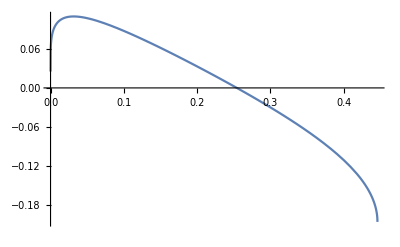

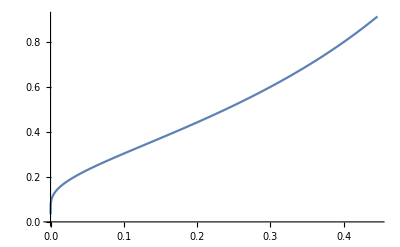

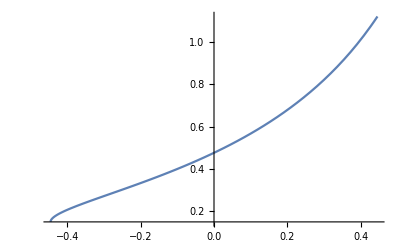

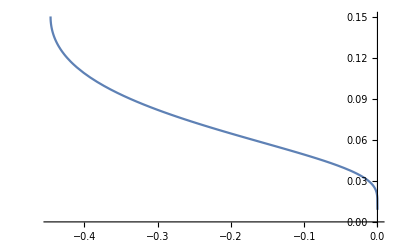

```mathematica
dif'[t_,p_] = D[dif[t,p],t]
dif''[t_,p_] = D[dif'[t,p],t]
difp[t_,p_] = D[dif[t,p],p]
ProductLog[1,0]

Plot[dif[t,2.1],{t,0,2*E^(-3/2)}]
Plot[gt[t,2.1],{t,0,2*E^(-3/2)}]
Plot[w0[t,2.1],{t,-2*E^(-3/2),2*E^(-3/2)}]
Plot[w1[t,2.1],{t,-2*E^(-3/2),0}]

(*Plot[dif'[t,2.1],{t,0,2*E^(-3/2)}]
Plot[dif''[t,2.1],{t,0,2*E^(-3/2)}]*)


(*ListAnimate[Table[Plot[difp[t/800,p],{p,2,4}],{t,1,100}]]
Plot[difp[.1,p],{p,2,4}]
ListAnimate[Table[Plot[dif[t,p],{t,0,2*E^(-3/2)}],{p,1,10}]]
ListAnimate[Table[Plot[difp[t,p],{t,0,2*E^(-3/2)}],{p,1,10}]]*)
```